```mathematica
Quit[]
```

total number of errors and warnings
===================================
fferr: no errors

```mathematica
$LoadFeynArts=True;
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.11 (2 Sep 2019) patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

```mathematica
$FAVerbose=0;
```

# Loop Contribution

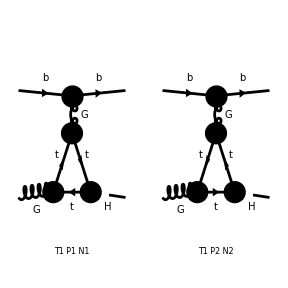

FeynArtsGraphics({b,G}→{b,H})(([T1 P1 N1] | [T1 P2 N2] | Null
Null | Null | Null
Null | Null | Null))

```mathematica
diagloop=InsertFields[CreateTopologies[1,2->2,ExcludeTopologies->{Tadpoles,SelfEnergies,AllBoxes}],{F[12],V[4]}->{F[12],S[1]},InsertionLevel->{Particles},Model->{"htt"},GenericModel->{"htt"},LastSelections->{V[4],F[9]}];
Paint[diagloop]
```

```mathematica
amploop=FCFAConvert[CreateFeynAmp[diagloop,Truncated->True],IncomingMomenta->{p[1],p[2]},OutgoingMomenta->{p[3],p[4]},LoopMomenta->{l},DropSumOver->True,UndoChiralSplittings->True,ChangeDimension->4]/.M$FACouplings/.{FAGS->gs,ybcky->yt,FCGV["MT"]->MT};
```

```mathematica
amploop=Plus@@amploop/.{DiracTrace->TR}//SUNSimplify//ChangeDimension[#,D]&//TID[#,l,ToPaVe->True]&//ChangeDimension[#,4]&//ReplaceAll[#,{D->4}]&//Simplify;
```

```mathematica
FCClearScalarProducts[]
SetMandelstam[s,t,u,p[1],p[2],-p[3],-p[4],MB,0,MB,MH];
amploop=amploop//Simplify;
```

```mathematica
Cases[amploop,_B0,Infinity]//DeleteDuplicates//StandardForm
```

{B0[MH^2,MT^2,MT^2],B0[t,MT^2,MT^2],B0[0,MT^2,MT^2]}

```mathematica
beta=Sqrt[4 MT^2/MH^2-1];
beta1=Sqrt[1-4 MT^2/t];
scalarIntegral={_C0->(1/2/(t-MH^2) (Log[(beta1+1)/(beta1-1)]^2+ ArcTan[2 beta/(1-beta^2)]^2)),
B0[MH^2,MT^2,MT^2]->(Log[m^2/MH^2]+2-beta ArcTan[2 beta/(beta^2-1)]-Log[(1+beta^2)/4]),
B0[t,MT^2,MT^2]->(Log[m^2/(-t)]+2+beta1 Log[beta1-1]-beta1 Log[beta1+1]-Log[(beta1^2-1)/4]),
B0[0,MT^2,MT^2]->(Log[m^2/MT^2])};
```

```mathematica
amploop=Series[amploop/.scalarIntegral,{ep,0,0}]//Simplify//PropagatorDenominatorExplicit//Normal
```

1/(8 √2 π^2 t (MH^2-t)^3)gs^3 MT yt T_Col3Col1^Glu2 (-1/2 ((tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2)))^2+log^2((√(1-(4 MT^2)/t)+1)/(√(1-(4 MT^2)/t)-1))) (2 (MH^2-t) (sin(al) (MH^2-t) (γ̄)^Lor3 ϵ^(Lor1Lor3 OverBar[p(2)]OverBar[p(4)])+cos(al) OverBar[p(2)]^Lor1 (MH^2+4 MT^2+t) γ̄·OverBar[p(4)])-2 cos(al) γ̄·OverBar[p(2)] (4 MH^2 (2 MT^2+t) OverBar[p(2)]^Lor1+(MH^2-t) OverBar[p(4)]^Lor1 (MH^2-4 MT^2-t))+cos(al) (MH^2-t)^2 (γ̄)^Lor1 (MH^2-4 MT^2-t))+4 cos(al) (MH^2-t) OverBar[p(2)]^Lor1 log(m^2/MT^2) ((MH^2+t) γ̄·OverBar[p(2)]+(t-MH^2) γ̄·OverBar[p(4)])+2 cos(al) (log(-m^2/t)+√(1-(4 MT^2)/t) log(√(1-(4 MT^2)/t)-1)-√(1-(4 MT^2)/t) log(√(1-(4 MT^2)/t)+1)-log(-MT^2/t)+2) (t (MH^2-t)^2 (γ̄)^Lor1-2 (MH^4+MH^2 t-2 t^2) OverBar[p(2)]^Lor1 γ̄·OverBar[p(4)]+2 γ̄·OverBar[p(2)] (t (t-MH^2) OverBar[p(4)]^Lor1+(MH^4+4 MH^2 t+t^2) OverBar[p(2)]^Lor1))-2 cos(al) (log(m^2/MH^2)-log(MT^2/MH^2)+√((4 MT^2)/MH^2-1) tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2))+2) (t (MH^2-t)^2 (γ̄)^Lor1+2 (-2 MH^4+MH^2 t+t^2) OverBar[p(2)]^Lor1 γ̄·OverBar[p(4)]+2 γ̄·OverBar[p(2)] (t (t-MH^2) OverBar[p(4)]^Lor1+2 (MH^4+2 MH^2 t) OverBar[p(2)]^Lor1)))

# Tree Contributions

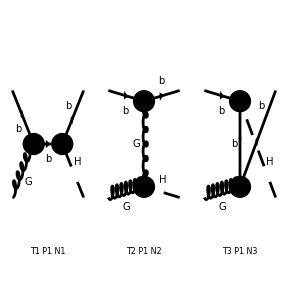

FeynArtsGraphics({b,G}→{b,H})(([T1 P1 N1] | [T2 P1 N2] | [T3 P1 N3]
Null | Null | Null
Null | Null | Null))

```mathematica
diagtree=InsertFields[CreateTopologies[0,2->2],{F[12],V[4]}->{F[12],S[1]},InsertionLevel->{Particles},Model->{"hbb"},GenericModel->{"hbb"}];
Paint[diagtree]
```

```mathematica
amptree=FCFAConvert[CreateFeynAmp[diagtree,Truncated->True],IncomingMomenta->{p[1],p[2]},OutgoingMomenta->{p[3],p[4]},DropSumOver->True,UndoChiralSplittings->True,ChangeDimension->4]/.M$FACouplings/.{FAGS->gs,ybcky->yb,al->be,FCGV["MB"]->MB};
```

```mathematica
amptree=amptree[[1]]+amptree[[3]]//Contract//PropagatorDenominatorExplicit//Simplify;
```

```mathematica
amptree
```

((s-MB^2) (ⅈ gs (γ̄)^Lor1 T_Col3Col1^Glu2).(γ̄·(OverBar[p(3)]-OverBar[p(2)])+MB).(yb (((γ̄)^6-(γ̄)^7) sin(be)-ⅈ ((γ̄)^6+(γ̄)^7) cos(be)))/(√2)+(u-MB^2) (yb (((γ̄)^6-(γ̄)^7) sin(be)-ⅈ ((γ̄)^6+(γ̄)^7) cos(be)))/(√2).(γ̄·(OverBar[p(3)]+OverBar[p(4)])+MB).(ⅈ gs (γ̄)^Lor1 T_Col3Col1^Glu2))/((MB^2-s) (MB^2-u))

# Square

```mathematica
spinsum[p_,h_]:=1/4 (1+h GA[5]).(GS[p]+MB).(1-h GA[5]);
```

```mathematica
ampsum=amploop+amptree;
ampS=-MT[Lor1,Lor2]spinsum[p[3],hf].ampsum.spinsum[p[1],hi].(ComplexConjugate[ampsum]/.{Lor1->Lor2,Lor3->Lor4})//PropagatorDenominatorExplicit//Contract//Simplify;
```

```mathematica
<<FeynCalcFormLink`
```

```mathematica
ampS=FeynCalcFormLink[DiracTrace[ampS]];
```

Symbols al,be,CA,CF,gs,hf,hi,MB,MH,MT,s,t,u,yb,yt;
Indices Lor2,Lor3,Lor4;
AutoDeclare Vector mom;
CFunctions B0,C0,p;
Format Mathematica;
L resFL = (-(CA*CF*gs^2*(hf*g5_(1)+gi_(1))*(MB*gi_(1)+g_(1,mom3))*(-(hf*g5_(1))+gi_(1))*
(-8*i_*yb*(g_(1,Lor2)*(MB-g_(1,mom2)+g_(1,mom3))*(-(i_*cos_(be)*(g6_(1)/2+g7_(1)/2))+(g6_(1)/2-g7_(1)/2)*sin_(be))/(MB^2-u)+
(-(i_*cos_(be)*(g6_(1)/2+g7_(1)/2))+(g6_(1)/2-g7_(1)/2)*sin_(be))*(MB+g_(1,mom3)+g_(1,mom4))*g_(1,Lor2)/(MB^2-s))-
(gs^2*MT*yt*(2*B0(MH^2,MT^2,MT^2)*cos_(al)*((MH^2-t)^2*t*g_(1,Lor2)-2*(2*MH^4-MH^2*t-t^2)*g_(1,mom4)*mom2(Lor2)+
2*g_(1,mom2)*(2*(MH^4+2*MH^2*t)*mom2(Lor2)-(MH^2-t)*t*mom4(Lor2)))-2*B0(t,MT^2,MT^2)*cos_(al)*
((MH^2-t)^2*t*g_(1,Lor2)-2*(MH^4+MH^2*t-2*t^2)*g_(1,mom4)*mom2(Lor2)+2*g_(1,mom2)*((MH^4+4*MH^2*t+t^2)*mom2(Lor2)-
(MH^2-t)*t*mom4(Lor2)))-(MH^2-t)*(4*B0(0,MT^2,MT^2)*cos_(al)*((MH^2+t)*g_(1,mom2)-(MH^2-t)*g_(1,mom4))*mom2(Lor2)+
C0(0,MH^2,t,MT^2,MT^2,MT^2)*((MH^2-t)^2*(MH^2-4*MT^2-t)*cos_(al)*g_(1,Lor2)-2*cos_(al)*g_(1,mom2)*
(4*MH^2*(2*MT^2+t)*mom2(Lor2)+(MH^2-t)*(MH^2-4*MT^2-t)*mom4(Lor2))+2*(MH^2-t)*((MH^2+4*MT^2+t)*cos_(al)*g_(1,mom4)*mom2(
Lor2)+(MH^2-t)*e_(Lor2,Lor3,mom2,mom4)*g_(1,Lor3)*sin_(al))))))/(pi_^2*(MH^2-t)^3*t))*(hi*g5_(1)+gi_(1))*
(MB*gi_(1)+g_(1,mom1))*(-(hi*g5_(1))+gi_(1))*
(8*i_*yb*(g_(1,Lor2)*(MB+g_(1,mom3)+g_(1,mom4))*(i_*cos_(be)*(g6_(1)/2+g7_(1)/2)-(g6_(1)/2-g7_(1)/2)*sin_(be))/(MB^2-s)+
(i_*cos_(be)*(g6_(1)/2+g7_(1)/2)-(g6_(1)/2-g7_(1)/2)*sin_(be))*(MB-g_(1,mom2)+g_(1,mom3))*g_(1,Lor2)/(MB^2-u))-
(gs^2*MT*yt*(2*B0(MH^2,MT^2,MT^2)*cos_(al)*((MH^2-t)^2*t*g_(1,Lor2)-2*(2*MH^4-MH^2*t-t^2)*g_(1,mom4)*mom2(Lor2)+
2*g_(1,mom2)*(2*(MH^4+2*MH^2*t)*mom2(Lor2)-(MH^2-t)*t*mom4(Lor2)))-2*B0(t,MT^2,MT^2)*cos_(al)*
((MH^2-t)^2*t*g_(1,Lor2)-2*(MH^4+MH^2*t-2*t^2)*g_(1,mom4)*mom2(Lor2)+2*g_(1,mom2)*((MH^4+4*MH^2*t+t^2)*mom2(Lor2)-
(MH^2-t)*t*mom4(Lor2)))-(MH^2-t)*(4*B0(0,MT^2,MT^2)*cos_(al)*((MH^2+t)*g_(1,mom2)-(MH^2-t)*g_(1,mom4))*mom2(Lor2)+
C0(0,MH^2,t,MT^2,MT^2,MT^2)*((MH^2-t)^2*(MH^2-4*MT^2-t)*cos_(al)*g_(1,Lor2)-2*cos_(al)*g_(1,mom2)*
(4*MH^2*(2*MT^2+t)*mom2(Lor2)+(MH^2-t)*(MH^2-4*MT^2-t)*mom4(Lor2))+2*(MH^2-t)*((MH^2+4*MT^2+t)*cos_(al)*g_(1,mom4)*mom2(
Lor2)+(MH^2-t)*e_(Lor2,Lor4,mom2,mom4)*g_(1,Lor4)*sin_(al))))))/(pi_^2*(MH^2-t)^3*t)))/2048);
trace4,1;
contract 0;
.sort;
#call put("%E", resFL)
#fromexternal

Piping the script to FORM and running FORM

Time needed by FORM : 6.191 seconds. FORM finished. Got the result back to Mathematica as a string.

Start translation to Mathematica / FeynCalc syntax

Total wall clock time used: 24.55 seconds. Translation to Mathematica and FeynCalc finished.

```mathematica
ampS
```

```mathematica
ampS=ampS//Contract//Simplify;
```

```mathematica
ampS
```

```mathematica
SetDirectory[NotebookDirectory[]];
ampS=Get["result.m"];
```

```mathematica
ampS=ampS/.scalarIntegral;
```

```mathematica
Clear[tmp];
Clear[e1];
tmp=Solve[e+Sqrt[e^2+MB^2]==Sqrt[e1^2+MB^2]+Sqrt[e1^2+MH^2],e1]//FullSimplify[#,MB>0 && MH>4 MB && e>0]&;
```

```mathematica
(*Kinematics*)
spd[x_,y_]:=x[[1]] y[[1]]-x[[2]] y[[2]]-x[[3]] y[[3]]-x[[4]] y[[4]];
eps[p[a_],p[b_],p[c_],p[d_]]:=Plus@@(q[a][[#[[1]]]] q[b][[#[[2]]]] q[c][[#[[3]]]] q[d][[#[[4]]]]&/@{{1,2,3,4},{1,3,4,2},{1,4,2,3},{2,1,4,3},{2,4,3,1},{2,3,1,4},{3,1,2,4},{3,2,4,1},{3,4,1,2},{4,1,3,2},{4,3,2,1},{4,2,1,3}})-Plus@@(q     [a][[#[[1]]]] q[b][[#[[2]]]] q[c][[#[[3]]]] q[d][[#[[4]]]]&/@{{1,3,2,4},{1,2,4,3},{1,4,3,2},{2,1,3,4},{2,3,4,1},{2,4,1,3},{3,1,4,2},{3,4,2,1},{3,2,1,4},{4,1,2,3},{4,2,3,1},{4,3,1,2}});
e1=e1/.tmp[[2]];
q[1]={Sqrt[e^2+MB^2],0,0,-e};(*pbin*)
q[2]={e,0,0,e};(*pgin*)
q[3]={Sqrt[e1^2+MB^2],e1 Sin[th],0,-e1 Cos[th]};(*pbout*)
q[4]={Sqrt[e1^2+MH^2],-e1 Sin[th],0,e1 Cos[th]};(*phiggs*)
(*q[5]={0,Sqrt[1/2],-Sqrt[1/2] I,0};(*pol+*)
q[6]={0,Sqrt[1/2],Sqrt[1/2] I,0};(*pol+ cc*)
q[7]={0,-Sqrt[1/2],-Sqrt[1/2] I,0};(*pol-*)
q[8]={0,-Sqrt[1/2],Sqrt[1/2] I,0};(*pol- cc*)
(*q[9]=2 lam1/MB {e,0,0,Sqrt[e^2+MB^2]};(*s for p[1]*)
q[10]=2 lam2/MB {e1,Sqrt[e1^2+MB^2] Sin[th],0,Sqrt[e1^2+MB^2] Cos[th]};(*s for p[3]*)*)
For[i=1,i<9,i++,
For[j=1,j<9,j++,
SP[p[i],p[j]]=spd[q[i],q[j]]//FullSimplify[#,MB<MH/4 && MB>0 && e>0]&;
]]*)
```

```mathematica
ampS=ampS//ReplaceAll[#,{s->spd[q[1]+q[2],q[1]+q[2]],t->spd[q[1]-q[3],q[1]-q[3]],u->spd[q[1]-q[4],q[1]-q[4]],Eps[Momentum[p[a_]],Momentum[p[b_]],Momentum[p[c_]],Momentum[p[d_]]]:>eps[p[a],p[b],p[c],p[d]]}]&;
```

```mathematica
Collect[ampS/.{MB->4.7,hi->1,hf->-1,MH->125,MT->172,e->(13000^2-4.7^2)/26000,CA->1,CF->1,m->1,gs->1,al->0,th->3.1415926},{yb,yt}]//Simplify
```

yb (yb (-1.40025×10^-16 cos(2 be)-1412.25)-4.76842×10^-15 yt cos(be))

```mathematica
Apply[f[#1,#2]&,{{1,1},{1,-1}},2]
```

{f(1,1),f(1,-1)}

```mathematica
ampTotal=Plus@@Apply[(ampS/.{MB->4.7,hi->#1,hf->#2,MH->125,MT->172,e->65,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1,m->1,gs->1})&,{{1,1},{1,-1},{-1,1},{-1,-1}},2];
```

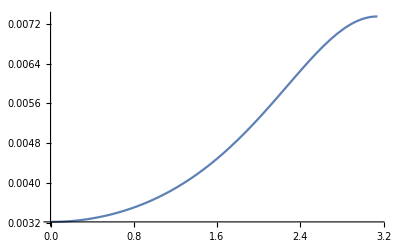

```mathematica
Plot[(ampTotal/.{be->0,yt->1,yb->4.7/246})-(ampTotal/.{be->Pi,yt->1,yb->4.7/246}),{th,0,Pi}]
```

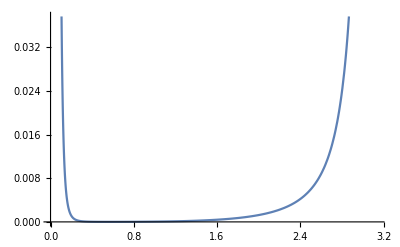

```mathematica
Plot[ampTotal/.{be->Pi,yt->1,yb->4.7/246},{th,0,Pi}]
```

```mathematica
ampS/.{MB->4.7,hi->1,hf->-1,MH->125,MT->172,e->(13000^2-4.7^2)/26000,CA->1,CF->1,m->1,gs->1,be->0,al->1,th->3.1415926}
```

6.17513×10^-74 (2.39263×10^21 yt (0.-1.69×10^8 (1.43561×10^28 yb+0.))+2.8561×10^16 (-1.0113×10^42 yb yt-5.33699×10^10 yb (1.50037×10^49 yb+4.61418×10^30 yt)+0.)+0.)

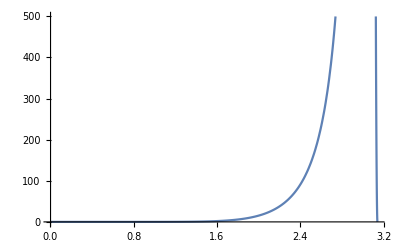

```mathematica
Plot[(ampS/.{MB->4.7,hi->1,hf->-1,MH->125,MT->172,e->(13000^2-4.7^2)/26000,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1,yb->4.7/246,m->1,gs->1,yt->1,be->0,al->0})/(ampS/.{MB->4.7,hi->1,hf->1,MH->125,MT->172,e->(13000^2-4.7^2)/26000,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1,yb->4.7/246,m->1,gs->1,yt->1,be->0,al->0}),{th,0.001,3.1415926}]
```

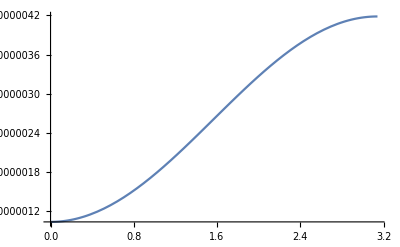

```mathematica
Plot[ampS*Sin[th]/.{MB->4.7,hi->1,hf->1,MH->125,MT->172,e->(13000^2-4.7^2)/26000,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1,yb->4.7/246,m->1,gs->1,yt->1,th->3,al->0},{be,0,Pi}]
```

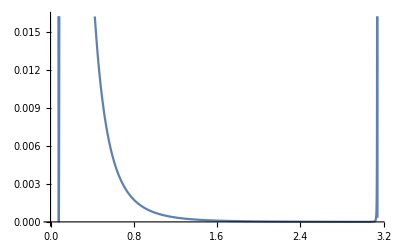

```mathematica
Plot[ampS*Sin[th]/.{MB->4.7,hi->1,hf->1,MH->125,MT->172,e->(13000^2-4.7^2)/26000,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1,yb->4.7/246,m->1,gs->1,yt->1,be->Pi,al->0},{th,0.00001,3.1415926}]
```

```mathematica
ampS*Sin[th]/.{MB->4.7,hi->1,hf->1,MH->125,MT->172,e->(13000^2-4.7^2)/26000,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1,yb->4.7/246,m->1,gs->1,yt->1,be->0,al->0,th->0}
```

0.

```mathematica
Plot[ampS/.{MB->4.7,hi->1,hf->-1,MH->125,MT->172,e->(13000^2-4.7^2)/26000,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1,yb->4.7/246,m->1,gs->1,yt->1,be->0,al->0},{th,0,Pi}]
```

```mathematica
result/.{MB->4.7,hi->1,hf->1,MH->125,MT->172,e->(13000^2-4.7^2)/26000,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1,yb->4.7/246,m->1,gs->1,yt->1,th->0}
```

1.15659×10^-41 (-3.78535×10^13 (-15625. (7.70682×10^29-1.47137×10^20 cos(be))-1.64812×10^24)+5.96857×10^17 (7.35686×10^19 cos(be)-7.70682×10^29)-2.44141×10^8 (3.65099×10^28 cos(be)-1.1395×10^-6 (1.6283×10^35 cos(be)+17.3874 (4.45938×10^20 cos(2 be)-4.45938×10^20))+6.88304×10^48)-6.23898×10^37)

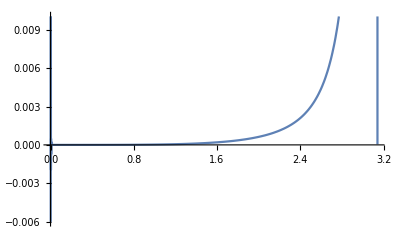

```mathematica
Plot[ampSp/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000,hi->1,hf->-1,ybcky->4.7/246,gs->1,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1},{th,0.,Pi}]
```

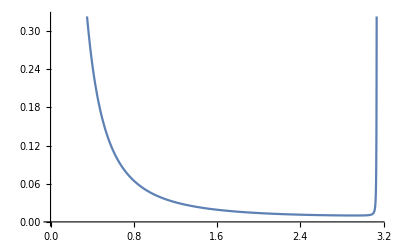

```mathematica
Plot[ampSm/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000,hi->-1,hf->-1,ybcky->4.7/246,gs->1,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1}//FullSimplify,{th,0,Pi}]
```